```mathematica
p[x_]=x^5-10 x^3+2
N[Solve[p[x]==0,x]]
```

2-10 x^3+x^5

{{x→-3.17217},{x→0.591794},{x→3.15216},{x→-0.285895-0.506208 ⅈ},{x→-0.285895+0.506208 ⅈ}}

1/10

t

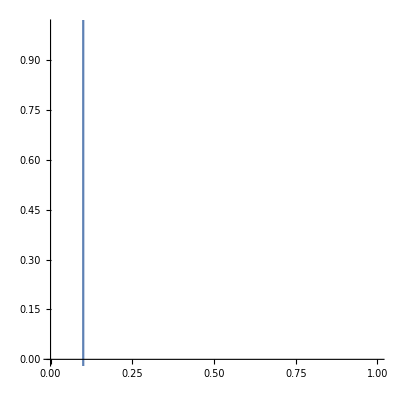

1/(10 (1/100+t^2))

-t/(1/100+t^2)

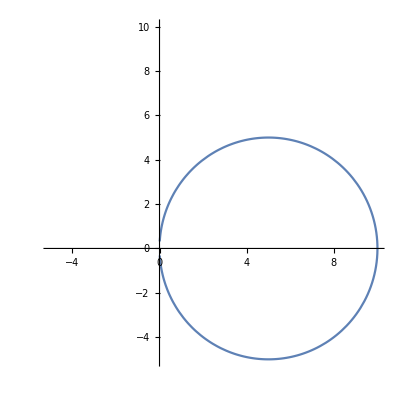

```mathematica
x[t_]=1/10
y[t_]=t
ParametricPlot[{x[t],y[t]},{t,-10,10},PlotRange->{0,1}]
x0[t_]=(1/10)/((1/10)^2+t^2)
y0[t_]=-t/((1/10)^2+t^2)
ParametricPlot[{x0[t],y0[t]},{t,-Pi,Pi},PlotRange->{-5,10}]
```

Cos[t]

Sin[t]

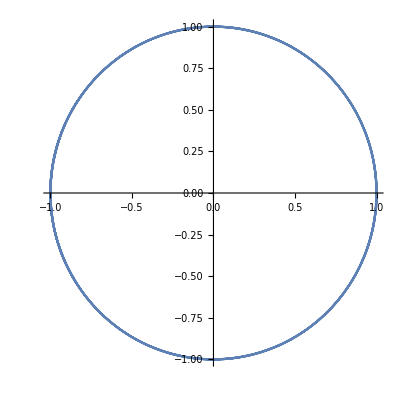

```mathematica
u[t_]=Cos[t]
v[t_]=Sin[t]
ParametricPlot[{u[t],v[t]},{t,-10,10}]
```

ⅇ^t Cos[1]

ⅇ^t Sin[1]

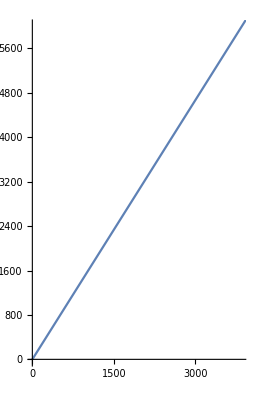

```mathematica
u0[t_]=Exp[t]*Cos[1]
v0[t_]=Exp[t]*Sin[1]
ParametricPlot[{u0[t],v0[t]},{t,0,10}]
```

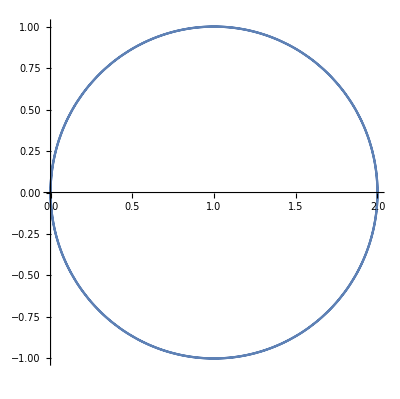

```mathematica
PolarPlot[2 Cos[t],{t,0,2 Pi}]
```



```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2 Pi}]
```

```mathematica
PolarPlot[2 Cos[t],{t,0, 2Pi}]
```

-Graphics-

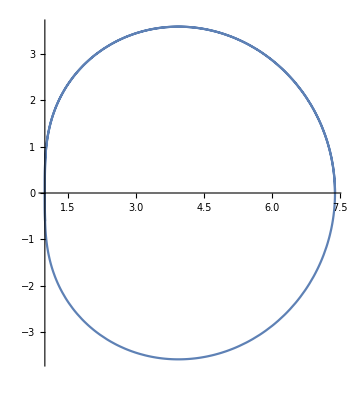

```mathematica
ParametricPlot[{Exp[1+Cos[t]]*Cos[Sin[t]],Exp[1+Cos[t]]*Sin[Sin[t]]},{t,0,10}]
```